# Binding Energy A

```mathematica
compoundMass = 252;
compoundCharge=98;
```

```mathematica
initialEnergy=QuantityMagnitude[compoundMass  IsotopeData[{compoundCharge,compoundMass}, "BindingEnergy"]];
```

## Systematics

```mathematica
sigZ = 0.62;
zWa[A_]:= compoundCharge/compoundMass A;
wWa[z_,A_]:= 1/(Sqrt[2 Pi ] sigZ) Exp[-(z- zWa[A])^2/(2 sigZ^2)];
```

## Calculations

```mathematica
tabTotE = Table[
{A,
QuantityMagnitude[(Sum[
(A IsotopeData[{Z,A}, "BindingEnergy"] + (252 - A) IsotopeData[{(compoundCharge - Z),(252-A)}, "BindingEnergy"] )wWa[Z,A],
{Z,Round[zWa[A]]-1,Round[zWa[A]]+1}])/(Sum[ wWa[Z,A],{Z,Round[zWa[A]-1],Round[zWa[A]+1]}])]- QuantityMagnitude[initialEnergy] },

{A,77,126}] ;

Export["tabTotE.txt",tabTotE]
```

tabTotE.txt

```mathematica
tabTotE2 = Table[
{A,
QuantityMagnitude[(Sum[
(QuantityMagnitude[A IsotopeData[{Z,A}, "BindingEnergy"] + (252 - A) IsotopeData[{(compoundCharge - Z),(252-A)}, "BindingEnergy"] ]- initialEnergy)^2wWa[Z,A],
{Z,Round[zWa[A]]-1,Round[zWa[A]]+1}])/(Sum[ wWa[Z,A],{Z,Round[zWa[A]-1],Round[zWa[A]+1]}])] },

{A,77,126}];
```

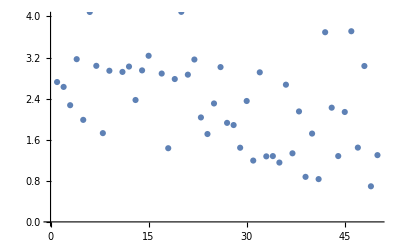

```mathematica
Sqrt[tabTotE2[[All,2]] - tabTotE[[All,2]]^2];
ListPlot[%,PlotRange->{0,4}]
```